```mathematica
img=-Graphics-;
xbits=Flatten[ImageData[Binarize[img]]];
```

```mathematica
size=ImageDimensions[img];
```

```mathematica
CanalZ[p_,bits_]:=Map[(If[#==1,If[Random[]<p,0,1],0])&,bits]
```

```mathematica
Manipulate[Image[Partition[ybits=CanalZ[p,xbits],size[[1]]]],{p,0,1,0.1}]
```

Part::partd: Part specification size⟦1⟧ is longer than depth of object.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[CanalZ[0,xbits],size⟦1⟧].

Image::imgarray: The specified argument Partition[CanalZ[0,xbits],size⟦1⟧] should be an array of rank 2 or 3 with machine-sized numbers.

Formula probabilidad de error

```mathematica
Pe[n_,p_]:=∑_(k=n+1)^(2*n+1) Binomial[2n+1,k]*p^k * (1-p)^(2*n+1-k)
Pe2[n_,p_]:=Binomial[2n+1,n+1]*p^(n+1)
```

```mathematica
Pe1[n_,p_]:=Binomial[2n+1,n+1]*p^(n+1)
```

```mathematica
Table[{n,Pe[n,0.3]},{n,1,20,1}]
```

{{1,0.216},{2,0.16308},{3,0.126036},{4,0.0988087},{5,0.0782248},{6,0.0623752},{7,0.0500125},{8,0.0402769},{9,0.0325534},{10,0.0263899},{11,0.021448},{12,0.0174697},{13,0.0142565},{14,0.0116538},{15,0.00954044},{16,0.00782066},{17,0.00641854},{18,0.00527348},{19,0.00433693},{20,0.0035699}}

```mathematica
a={1,0,1,0};
```

Codificación por repetición

```mathematica
Codif[bits_,n_]:=Flatten[Map[(Table[#,2*n+1])&,bits]]
```

```mathematica
CanalZ[0.1,Codif[a,1]]
```

{1,1,1,0,0,0,1,1,1,0,0,0}

```mathematica
DecoMay[bits_,n_]:=Map[(If [Count[#,1]<=n,0,1])&,Partition[bits,2n+1]]
```

```mathematica
Manipulate[Image[Partition[ybits=DecoMay[CanalZ[p,Codif[xbits,n]],n],size[[1]]]],{p,0,1,0.1},{n,1,15,1}]
```

Part::partd: Part specification size⟦1⟧ is longer than depth of object.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[DecoMay[CanalZ[0,Codif[xbits,1]],1],size⟦1⟧].

Image::imgarray: The specified argument Partition[DecoMay[CanalZ[0,Codif[xbits,1]],1],size⟦1⟧] should be an array of rank 2 or 3 with machine-sized numbers.

```mathematica
HammingDistance[xbits,ybits]/Length[xbits]//N
```

0.

```mathematica
H[p_]:=If[p==0||p==1,0,p*Log[2,1/p]+(1-p)*Log[2,1/(1-p)]]
```

```mathematica
HFull[lst_]:=If[Total[lst]==1,Map[(#*Log[2,1/#])&,lst],0]
```

Calcular N según Pe

```mathematica
Pe[n_,p_]:=∑_(k=n+1)^(2n+1) Binomial[2n+1,k]*p^k*(1-p)^(2n+1-k)
```

```mathematica
Table[{n,Pe[n,0.25]},{n,0,10,1}]
```

{{0,0.25},{1,0.15625},{2,0.103516},{3,0.0705566},{4,0.0489273},{5,0.0343275},{6,0.0242901},{7,0.0172998},{8,0.0123848},{9,0.00890328},{10,0.00642271}}

Curva

```mathematica
R[pe_,p_]:=(1-H[p])/(1-H[pe])
```

```mathematica
g=Plot[R[pe,0.1],{pe,0,0.5}];
```

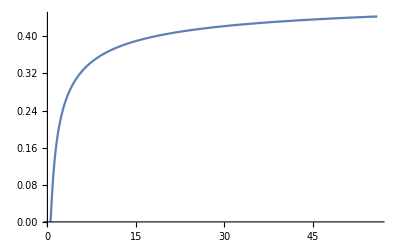

```mathematica
Show[g/. x_Line:>Reverse[x,3],PlotRange->Automatic]
```

## Que pasaría al pasar dos veces por el canal Z?

```mathematica
Manipulate[Row[
Image[Partition[y2bits=DecoMay[CanalZ[p,CanalZ[p,Codif[xbits,n]]],n],size[[1]]]],
Image[Partition[y1bits=DecoMay[CanalZ[p,Codif[xbits,n]],n],size[[1]]]]
],{p,0,1,0.1},{n,1,15,1}]
```

Part::partd: Part specification size⟦1⟧ is longer than depth of object.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[DecoMay[CanalZ[0,CanalZ[0,Codif[xbits,1]]],1],size⟦1⟧].

Image::imgarray: The specified argument Partition[DecoMay[CanalZ[0,CanalZ[0,Codif[xbits,1]]],1],size⟦1⟧] should be an array of rank 2 or 3 with machine-sized numbers.

Part::partd: Part specification size⟦1⟧ is longer than depth of object.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[DecoMay[CanalZ[0,Codif[xbits,1]],1],size⟦1⟧].

Image::imgarray: The specified argument Partition[DecoMay[CanalZ[0,Codif[xbits,1]],1],size⟦1⟧] should be an array of rank 2 or 3 with machine-sized numbers.